```mathematica
f[φ_]=-(9 φ^4-12 φ^3+30 φ^2-12 φ+1)/3;
g[φ_]=-2 (27 φ^6-54 φ^5-135 φ^4+180 φ^3-99 φ^2+18 φ-1)/27;
```

```mathematica
Δ[φ_]=-16(4 f[φ]^3+27 g[φ]^2);
```

```mathematica
Δ[φ]//FullSimplify
(*Ok! ChatGPT was right.*)
```

4096 (-1+φ)^3 φ^6 (-1+9 φ)

```mathematica
(*Define the moebius map that sends phi into an isogenous phi. Note: Moebius is not SL(2,ℤ)! But SL(2,ℤ) sits inside Moebius(ℂ).*)
mob[x_]=(x-1)/(9x-1);
```

```mathematica
Solve[mob[x]==x,x]
```

{{x→1/9 (1-2 ⅈ √2)},{x→1/9 (1+2 ⅈ √2)}}

```mathematica
mob[mob[x]]==x//FullSimplify
```

True

```mathematica
Δ[mob[x]]//FullSimplify
```

(16777216 (-1+x)^6 x^3)/(1-9 x)^10

```mathematica
Solve[Δ[mob[x]]==Δ[x],x]
```

{{x→0},{x→0},{x→0},{x→1},{x→1},{x→1},{x→1/9 (1-2 ⅈ √2)},{x→1/9 (1+2 ⅈ √2)},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

```mathematica
a[φ_,α_]:=-α*φ^4+324*φ^3-810*φ^2+324*φ-27
b[φ_]:=-1458*φ^6+2916*φ^5+7290*φ^4-9720*φ^3+5346*φ^2-972*φ+54
Delta[phi_,α_]:=-16(4 a[phi,α]^3+27 b[phi]^2);
Delta[x,y]//FullSimplify
N[Delta[1,243]]
```

-16 (78732 (1-3 x (2+x))^2 (1+3 x (-4+x (10+3 (-4+x) x)))^2-4 (27-162 (-2+x) x (-1+2 x)+x^4 y)^3)

0.

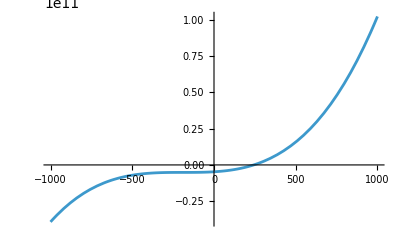

```mathematica
Plot[Delta[1,x],{x,-1000,1000}]
```

```mathematica
Delta[3,x]//FullSimplify
```

-16 (9755209728+4 (2403-81 x)^3)

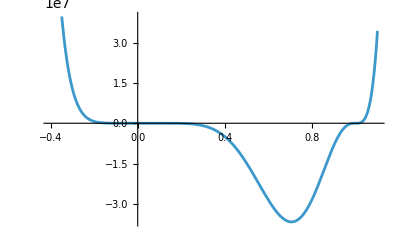

```mathematica
Plot[Delta[x,243],{x,-0.4,1.1}]
```

```mathematica
Delta[1/25,243]
```

481469424205824/95367431640625